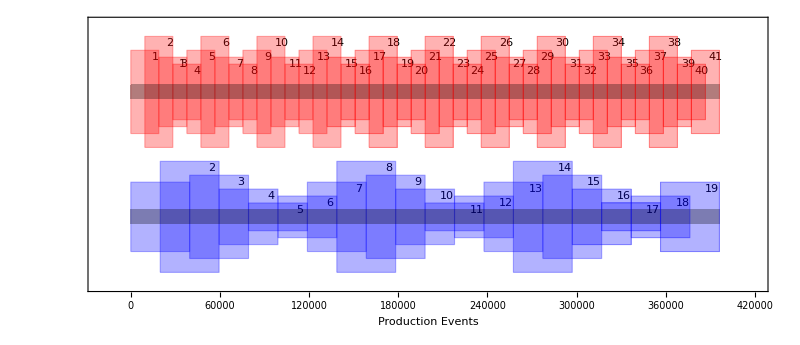

```mathematica
dif=90000;
x1=39610;
set1={39610,79220,118830,158440,198050,237660,277270,316880,356490,396096};
comp=Table[{{{Opacity@1,Text[xa,{x[[1,2]]-x1/8,95000}]},{EdgeForm@Dashed,Opacity[0.3],Blue,Rectangle[{x[[1,1]],20000},{x[[1,2]],100000}]}},{{Opacity@1,Text[xb,{x[[2,2]]-x1/8,85000}]},{EdgeForm@Dashed,Opacity[0.3],Blue,Rectangle[{x[[2,1]],30000},{x[[2,2]],90000}]}},{{Opacity@1,Text[xc,{x[[3,2]]-x1/8,75000}]},{EdgeForm@Dashed,Opacity[0.3],Blue,Rectangle[{x[[3,1]],40000},{x[[3,2]],80000}]}},{{Opacity@1,Text[xd,{x[[4,2]]-x1/8,65000}]},{EdgeForm@Dashed,Opacity[0.3],Blue,Rectangle[{x[[4,1]],50000},{x[[4,2]],70000}]}},{{Opacity@1,Text[xe,{x[[5,2]]-x1/8,70000}]},{EdgeForm@Dashed,Opacity[0.3],Blue,Rectangle[{x[[5,1]],45000},{x[[5,2]],75000}]}},{{Opacity@1,Text[xf,{x[[6,2]]-x1/8,80000}]},{EdgeForm@Dashed,Opacity[0.3],Blue,Rectangle[{x[[6,1]],35000},{x[[6,2]],85000}]}}},{x,Partition[Flatten[Table[{{z[[1]]-x1/2,z[[2]]-x1/2},{z[[1]],z[[2]]}},{z,
Partition[set1,2,1]}],1],6]}];
x2=18862;
set2={18862,37724,56586,75448,94310,113172,132034,150896,169758,188620,207482,226344,245206,264068,282930,301792,320654,339516,358378,377240,396096};
comp2=Table[{{{Opacity@1,Text[xaa,{x[[1,2]]-x2/8,95000+dif}]},{EdgeForm@Dashed,Opacity[0.3],Red,Rectangle[{x[[1,1]],20000+dif},{x[[1,2]],100000+dif}]}},{{Opacity@1,Text[xbb,{x[[2,2]]-x2/8,80000+dif}]},{EdgeForm@Dashed,Opacity[0.3],Red,Rectangle[{x[[2,1]],35000+dif},{x[[2,2]],85000+dif}]}},{{Opacity@1,Text[xcc,{x[[3,2]]-x2/8,75000+dif}]},{EdgeForm@Dashed,Opacity[0.3],Red,Rectangle[{x[[3,1]],40000+dif},{x[[3,2]],80000+dif}]}},{{Opacity@1,Text[xdd,{x[[4,2]]-x2/8,85000+dif}]},{EdgeForm@Dashed,Opacity[0.3],Red,Rectangle[{x[[4,1]],30000+dif},{x[[4,2]],90000+dif}]}}},{x,Partition[Flatten[Table[{{z[[1]]-x2/2,z[[2]]-x2/2},{z[[1]],z[[2]]}},{z,
Partition[set2,2,1]}],1],4]}];
Graphics[{{Join[{{Opacity@1,Text[1,{First@set1-x1/8,80000+dif}]},{EdgeForm@Dashed,Opacity[0.3],Blue,Rectangle[{1,35000},{First@set1,85000}]}},
Join[Flatten[comp[[1]]/.Flatten@MapThread[{#1->#2}&,{{xa,xb,xc,xd,xe,xf},{2,3,4,5,6,7}}],1],Flatten[comp[[2]]/.Flatten@MapThread[{#1->#2}&,{{xa,xb,xc,xd,xe,xf},{8,9,10,11,12,13}}],1],Flatten[comp[[3]]/.Flatten@MapThread[{#1->#2}&,{{xa,xb,xc,xd,xe,xf},{14,15,16,17,18,19}}],1]]],{Opacity[0.3],Black,Rectangle[{1,55000},{Last@set1,65000}]}},{Join[{{Opacity@1,Text[1,{First@set2-x2/8,85000+dif}]},{EdgeForm@Dashed,Opacity[0.3],Red,Rectangle[{1,30000+dif},{First@set2,90000+dif}]}},
Join[Flatten[comp2[[1]]/.Flatten@MapThread[{#1->#2}&,{{xaa,xbb,xcc,xdd},{2,3,4,5}}],1],Flatten[comp2[[2]]/.Flatten@MapThread[{#1->#2}&,{{xaa,xbb,xcc,xdd},{6,7,8,9}}],1],Flatten[comp2[[3]]/.Flatten@MapThread[{#1->#2}&,{{xaa,xbb,xcc,xdd},{10,11,12,13}}],1],Flatten[comp2[[4]]/.Flatten@MapThread[{#1->#2}&,{{xaa,xbb,xcc,xdd},{14,15,16,17}}],1],Flatten[comp2[[5]]/.Flatten@MapThread[{#1->#2}&,{{xaa,xbb,xcc,xdd},{18,19,20,21}}],1],Flatten[comp2[[6]]/.Flatten@MapThread[{#1->#2}&,{{xaa,xbb,xcc,xdd},{22,23,24,25}}],1],Flatten[comp2[[7]]/.Flatten@MapThread[{#1->#2}&,{{xaa,xbb,xcc,xdd},{26,27,28,29}}],1],Flatten[comp2[[8]]/.Flatten@MapThread[{#1->#2}&,{{xaa,xbb,xcc,xdd},{30,31,32,33}}],1],Flatten[comp2[[9]]/.Flatten@MapThread[{#1->#2}&,{{xaa,xbb,xcc,xdd},{34,35,36,37}}],1],Flatten[comp2[[10]]/.Flatten@MapThread[{#1->#2}&,{{xaa,xbb,xcc,xdd},{38,39,40,41}}],1]]],{Opacity[0.3],Black,Rectangle[{1,55000+dif},{Last@set2,65000+dif}]}}},Frame->True,PlotRange->{{-20000,420000},{10000,200000}},FrameTicks->{{None,None},{All,All}},FrameLabel->"Production Events",ImageSize->800]
```

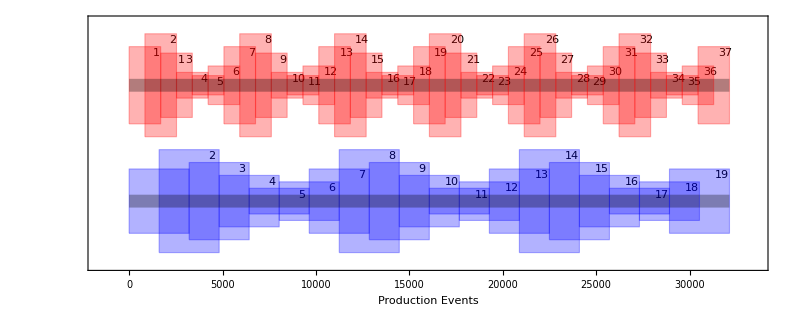

```mathematica
dif=9000;
x1=3214;
set1={3214,6428,9642,12856,16070,19284,22498,25712,28926,32138};
comp=Table[{{{Opacity@1,Text[xa,{x[[1,2]]-x1/8,9500}]},{EdgeForm@Dashed,Opacity[0.3],Blue,Rectangle[{x[[1,1]],2000},{x[[1,2]],10000}]}},{{Opacity@1,Text[xb,{x[[2,2]]-x1/8,8500}]},{EdgeForm@Dashed,Opacity[0.3],Blue,Rectangle[{x[[2,1]],3000},{x[[2,2]],9000}]}},{{Opacity@1,Text[xc,{x[[3,2]]-x1/8,7500}]},{EdgeForm@Dashed,Opacity[0.3],Blue,Rectangle[{x[[3,1]],4000},{x[[3,2]],8000}]}},{{Opacity@1,Text[xd,{x[[4,2]]-x1/8,6500}]},{EdgeForm@Dashed,Opacity[0.3],Blue,Rectangle[{x[[4,1]],5000},{x[[4,2]],7000}]}},{{Opacity@1,Text[xe,{x[[5,2]]-x1/8,7000}]},{EdgeForm@Dashed,Opacity[0.3],Blue,Rectangle[{x[[5,1]],4500},{x[[5,2]],7500}]}},{{Opacity@1,Text[xf,{x[[6,2]]-x1/8,8000}]},{EdgeForm@Dashed,Opacity[0.3],Blue,Rectangle[{x[[6,1]],3500},{x[[6,2]],8500}]}}},{x,Partition[Flatten[Table[{{z[[1]]-x1/2,z[[2]]-x1/2},{z[[1]],z[[2]]}},{z,
Partition[set1,2,1]}],1],6]}];
x2=1692;
set2={1692,3384,5076,6768,8460,10152,11844,13536,15228,16920,18612,20304,21996,23688,25380,27072,28764,30456,32138};
comp2=Table[{{{Opacity@1,Text[xaa,{x[[1,2]]-x2/8,9500+dif}]},{EdgeForm@Dashed,Opacity[0.3],Red,Rectangle[{x[[1,1]],2000+dif},{x[[1,2]],10000+dif}]}},{{Opacity@1,Text[xbb,{x[[2,2]]-x2/8,8000+dif}]},{EdgeForm@Dashed,Opacity[0.3],Red,Rectangle[{x[[2,1]],3500+dif},{x[[2,2]],8500+dif}]}},{{Opacity@1,Text[xcc,{x[[3,2]]-x2/8,6500+dif}]},{EdgeForm@Dashed,Opacity[0.3],Red,Rectangle[{x[[3,1]],5000+dif},{x[[3,2]],7000+dif}]}},{{Opacity@1,Text[xdd,{x[[4,2]]-x2/8,6250+dif}]},{EdgeForm@Dashed,Opacity[0.3],Red,Rectangle[{x[[4,1]],5250+dif},{x[[4,2]],6750+dif}]}},{{Opacity@1,Text[xee,{x[[5,2]]-x2/8,7000+dif}]},{EdgeForm@Dashed,Opacity[0.3],Red,Rectangle[{x[[5,1]],4500+dif},{x[[5,2]],7500+dif}]}},{{Opacity@1,Text[xff,{x[[6,2]]-x2/8,8500+dif}]},{EdgeForm@Dashed,Opacity[0.3],Red,Rectangle[{x[[6,1]],3000+dif},{x[[6,2]],9000+dif}]}}},{x,Partition[Flatten[Table[{{z[[1]]-x2/2,z[[2]]-x2/2},{z[[1]],z[[2]]}},{z,
Partition[set2,2,1]}],1],6]}];
Graphics[{{Join[{{Opacity@1,Text[1,{First@set1-x1/8,8000+dif}]},{EdgeForm@Dashed,Opacity[0.3],Blue,Rectangle[{1,3500},{First@set1,8500}]}},
Join[Flatten[comp[[1]]/.Flatten@MapThread[{#1->#2}&,{{xa,xb,xc,xd,xe,xf},{2,3,4,5,6,7}}],1],Flatten[comp[[2]]/.Flatten@MapThread[{#1->#2}&,{{xa,xb,xc,xd,xe,xf},{8,9,10,11,12,13}}],1],Flatten[comp[[3]]/.Flatten@MapThread[{#1->#2}&,{{xa,xb,xc,xd,xe,xf},{14,15,16,17,18,19}}],1]]],{Opacity[0.3],Black,Rectangle[{1,5500},{Last@set1,6500}]}},{Join[{{Opacity@1,Text[1,{First@set2-x2/8,8500+dif}]},{EdgeForm@Dashed,Opacity[0.3],Red,Rectangle[{1,3000+dif},{First@set2,9000+dif}]}},
Join[Flatten[comp2[[1]]/.Flatten@MapThread[{#1->#2}&,{{xaa,xbb,xcc,xdd,xee,xff},{2,3,4,5,6,7}}],1],Flatten[comp2[[2]]/.Flatten@MapThread[{#1->#2}&,{{xaa,xbb,xcc,xdd,xee,xff},{8,9,10,11,12,13}}],1],Flatten[comp2[[3]]/.Flatten@MapThread[{#1->#2}&,{{xaa,xbb,xcc,xdd,xee,xff},{14,15,16,17,18,19}}],1],Flatten[comp2[[4]]/.Flatten@MapThread[{#1->#2}&,{{xaa,xbb,xcc,xdd,xee,xff},{20,21,22,23,24,25}}],1],Flatten[comp2[[5]]/.Flatten@MapThread[{#1->#2}&,{{xaa,xbb,xcc,xdd,xee,xff},{26,27,28,29,30,31}}],1],Flatten[comp2[[6]]/.Flatten@MapThread[{#1->#2}&,{{xaa,xbb,xcc,xdd,xee,xff},{32,33,34,35,36,37}}],1]]],{Opacity[0.3],Black,Rectangle[{1,5500+dif},{Last@set2,6500+dif}]}}},Frame->True,PlotRange->{{-1500,33500},{1000,20000}},FrameTicks->{{None,None},{All,All}},FrameLabel->"Production Events",ImageSize->800,AspectRatio->2/5]
```